```mathematica
N0=100;
wa=1;
tau=65;
shift=Pi/wa;
range=70;

f[x_]:=N0*Exp[-x/tau]*(1+.4*Cos[wa*x]);
U[x_]:=.25*f[x+shift]+.25*f[x-shift];
V[x_]:=2*.25*f[x];
R[x_]:=(V[x]-U[x])/(V[x]+U[x])

(*Rasterize[Plot[{f[x]},{x,0,range}, PlotLegends->Placed[{"N(t)"},{0.8,0.8}]],RasterSize->1000]
Rasterize[Plot[{V[x], U[x]},{x,0,range}, PlotLegends->Placed[{"V(t)","U(t)"},{0.8,0.8}]],RasterSize->1000]
Rasterize[Plot[V[x]-U[x],{x,0,range},PlotLegends->Placed["V(t) - U(t)",{0.8,0.8}]],RasterSize->1000]
Rasterize[Plot[V[x]+U[x],{x,0,range},PlotLegends->Placed["V(t) + U(t)",{0.8,0.8}]],RasterSize->1000]
Rasterize[Plot[R[x],{x,0,range},PlotLegends->Placed["R(t)",{0.8,0.8}]],RasterSize->1000]*)

Rasterize[Plot[{f[x]},{x,0,range},PlotLegends->LineLegend[{"N(t)"},LabelStyle->{FontFamily->"Courier",18},LegendFunction ->(Framed[#,FrameMargins->0,Background->White]&)
]~Placed~{0.75,0.8}],RasterSize->1000,ImageSize->1000]
Rasterize[Plot[{V[x], U[x]},{x,0,range},PlotLegends->LineLegend[{"V(t)","U(t)"},LabelStyle->{FontFamily->"Courier",18},LegendFunction->Framed
]~Placed~{0.75,0.8}]]
Rasterize[Plot[{V[x]-U[x]},{x,0,range},PlotLegends->LineLegend[{"V(t) - U(t)"},LabelStyle->{FontFamily->"Courier",18},LegendFunction ->(Framed[#,FrameMargins->0,Background->White]&)
]~Placed~{0.75,0.8}]]
Rasterize[Plot[{V[x]+U[x]},{x,0,range},PlotLegends->LineLegend[{"V(t) + U(t)"},LabelStyle->{FontFamily->"Courier",18},LegendFunction ->(Framed[#,FrameMargins->0,Background->White]&)
]~Placed~{0.75,0.8}]]
Rasterize[Plot[{R[x]},{x,0,range},PlotLegends->LineLegend[{"R(t)"},LabelStyle->{FontFamily->"Courier",18},LegendFunction ->(Framed[#,FrameMargins->0,Background->White]&)
]~Placed~{0.75,0.8}]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

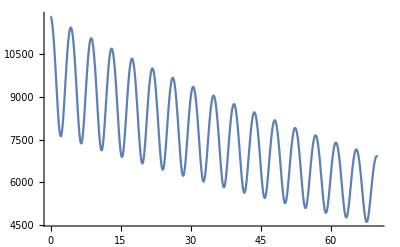

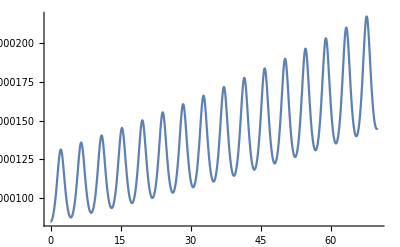

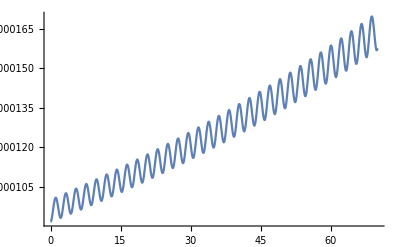

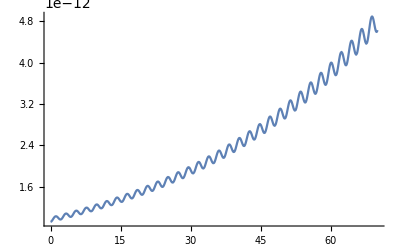

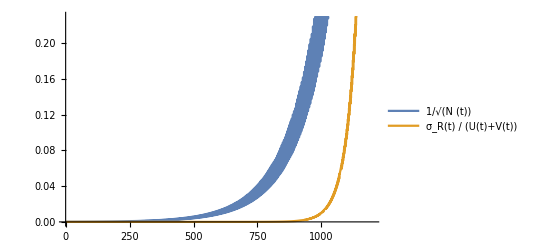

```mathematica
Plot[{Sqrt[f[x]]},{x,0,70},PlotLegends->"√(N (t))"]
Plot[{Sqrt[f[x]]/f[x]},{x,0,70},PlotLegends->"1/√(N (t))"]
Plot[{Sqrt[(1-R[x]^2)/(V[x]+U[x])]},{x,0,70},PlotLegends->"σ_R(t)"]
Plot[{Sqrt[(1-R[x]^2)/(V[x]+U[x])]/(V[x]+U[x])},{x,0,70},PlotLegends->"σ_R(t)/(U(t)+V(t))"]
Plot[{Sqrt[f[x]]/f[x], Sqrt[(1-R[x]^2)/(V[x]+U[x])]
/(V[x]+U[x])},{x,0,1200},PlotLegends->{"1/√(N (t))", "σ_R(t) / (U(t)+V(t))"}]
```

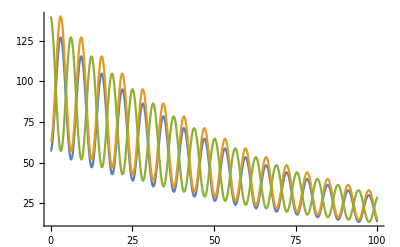

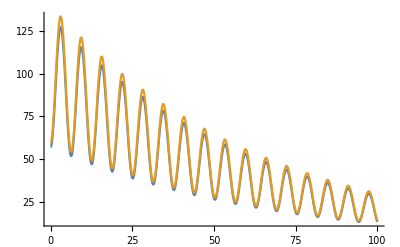

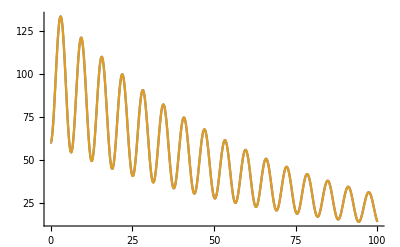

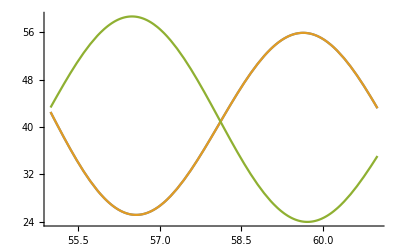

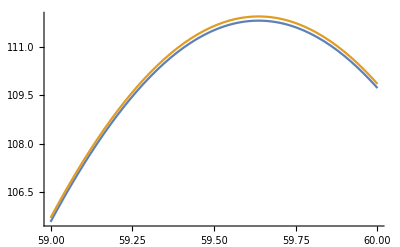

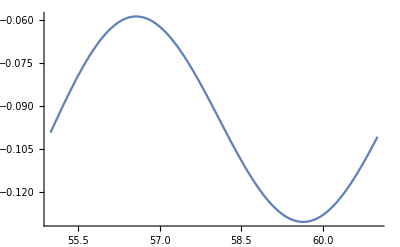

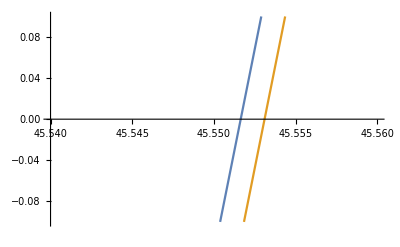

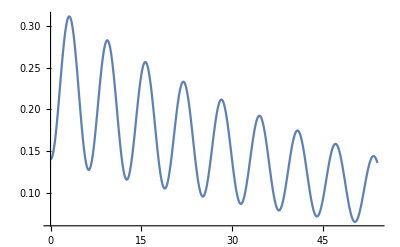

```mathematica
Plot[{f[x+shift],f[x-shift],f[x]},{x,0,100}]
Plot[{f[x+shift], f[x+shift]*Exp[shift/tau]},{x,0,100}]
Plot[{ f[x+shift]*Exp[shift/tau], f[x-shift]*Exp[-shift/tau]},{x,0,100}]
Plot[{ f[x+shift]*Exp[shift/tau], f[x-shift]*Exp[-shift/tau], f[x]},{x,55,61}]
Plot[{ f[x+shift]*Exp[shift/tau]+ f[x-shift]*Exp[-shift/tau], f[x+shift]+ f[x-shift]},{x,59,60}]
Plot[{(f[x+shift]*Exp[shift/tau]+ f[x-shift]*Exp[-shift/tau])-( f[x+shift]+ f[x-shift])},{x,55,61}]

Plot[{f[x+shift]+f[x-shift]- 2*f[x],f[x+shift]*Exp[shift/tau]+ f[x-shift]*Exp[-shift/tau]- 2*f[x]},{x,45.54,45.56},PlotRange->{-.1,.1}]
Plot[{(f[x+shift]+f[x-shift]- 2*f[x])-(f[x+shift]*Exp[shift/tau]+ f[x-shift]*Exp[-shift/tau]- 2*f[x])},{x,0,54}]
```

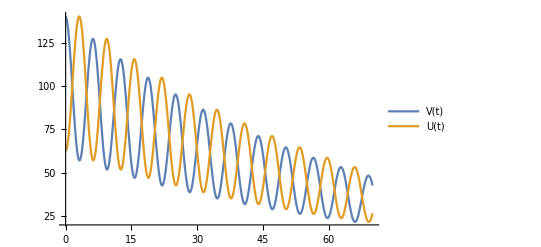

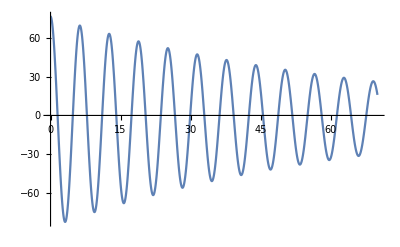

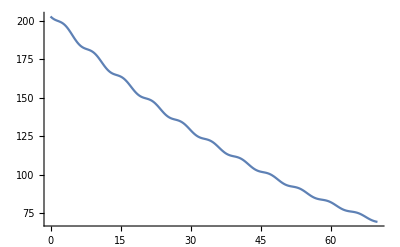

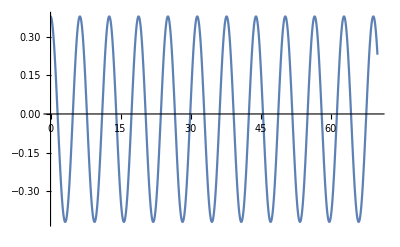

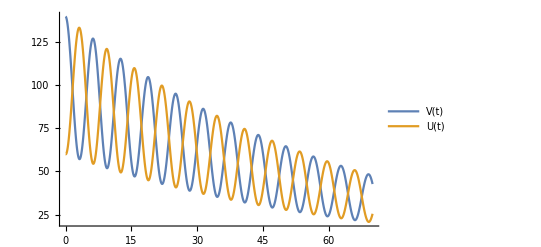

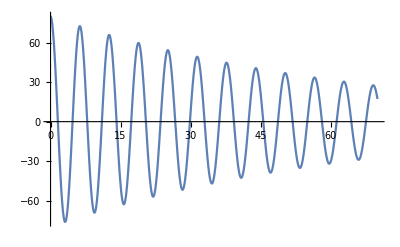

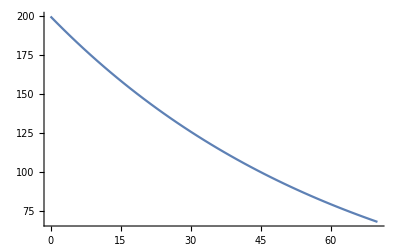

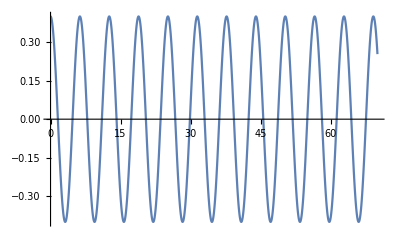

```mathematica
UU[x_]:=f[x-shift];
VV[x_]:=f[x];

Plot[{VV[x], UU[x]},{x,0,range}, PlotLegends->{"V(t)","U(t)"}]
Plot[VV[x]-UU[x],{x,0,range},PlotLegends->"V(t) - U(t)"]
Plot[VV[x]+UU[x],{x,0,range},PlotLegends->"V(t) + U(t)"]
Plot[(VV[x]-UU[x])/(VV[x]+UU[x]),{x,0,range},PlotLegends->"(V(t) - U(t))/ (V(t) + U(t))"]

UU[x_]:=f[x-shift]*Exp[-shift/tau];
VV[x_]:=f[x];

Plot[{VV[x], UU[x]},{x,0,range}, PlotLegends->{"V(t)","U(t)"}]
Plot[VV[x]-UU[x],{x,0,range},PlotLegends->"V(t) - U(t)"]
Plot[VV[x]+UU[x],{x,0,range},PlotLegends->"V(t) + U(t)"]
Plot[(VV[x]-UU[x])/(VV[x]+UU[x]),{x,0,range},PlotLegends->"(V(t) - U(t)) / (V(t) + U(t))"]
```